# MagnusExpansionTerm

Generate the nth term in the Magnus expansion of a time-dependent operator

## Definition

Define two functions, one for calculating d(σ) and the other one to calculate the coefficient c_n=(-1)^(d(σ))/(n (n-1
d(σ))):

```mathematica
ClearAll[descentCount,coeff];
descentCount[σ_List]:=Total[Clip[Differences[σ],{0,0},{1,0}]];
coeff[n_,σ_List]:=With[{d=descentCount[σ]},(-1)^d/(n Binomial[n-1,d])]
```

Define actual function:

```mathematica
ClearAll[MagnusExpansionTerm]
Options[MagnusExpansionTerm]={"CommutatorForm"->True,"TimeIntegration"->False,"Reduce"->None};

MagnusExpansionTerm[n_,op_,opts:OptionsPattern[]]:=MagnusExpansionTerm[n,op,Nothing,opts]

MagnusExpansionTerm[n_,op_,alg_,OptionsPattern[]]:=Module[{σList=Permutations[Range[n-1]],ΩCommutator},
ΩCommutator=Sum[coeff[n,j]Fold[If[OptionValue["CommutatorForm"],HoldForm[Commutator[#2,#1]]&,Commutator[#2,#1,alg]&],
op[Subscript[t, #]]&/@Reverse[Join[j,{n}]]],{j,σList}];
If[OptionValue["TimeIntegration"],Integrate[If[MatchQ[OptionValue["Reduce"],None],ΩCommutator,OptionValue["Reduce"][ΩCommutator]],Sequence@@Table[{Subscript[t, i],0,If[i==1,t,Subscript[t, i-1]]},{i,n}]],If[MatchQ[OptionValue["Reduce"],None],ΩCommutator,OptionValue["Reduce"][ΩCommutator]]]]
```

## Documentation

### Usage

MagnusExpansionTerm[n,op]

generates the order-n term in the Magnus expansion of the operator op.

MagnusExpansionTerm[n,op,alg]

generates the order-n term in the Magnus expansion of the operator op, for the algebraic operation alg, which can be Dot, Composition, TensorProduct or NonCommutativeMultiply.

MagnusExpansionTerm[n, op, alg,"CommutatorForm"->True]

generates the order-n term in the Magnus expansion of the operator op, for the algebraic operation alg, while holding the commutation form.

MagnusExpansionTerm[n, op, alg,"TimeIntegration"->True]

generates the time-integrated order-n term in the Magnus expansion of the operator op, for the algebraic operation alg.

MagnusExpansionTerm[n, op, alg,"Reduce"->f]

generates the order-n term in the Magnus expansion of the operator op, for the algebraic operation alg, after reduction of polynomial using f.

### Details & Options

Magnus terms?  Is that a type of Magnus expansion?  Explain where Magnus comes from.  Also, the Check / Validate reveals many items, such as not filling in your author name. Please address these items.

The main goal is to solve (ⅆY(t))/ⅆt=A(t)Y(t) with Y(0)=I, where in general  [A(t_1),A(t_2)]≠0. The exact solution can be written as Y(t)=e^(Ω(t)). The Magnus expansion expresses Ω(t) as an infinite series of time-ordered integrals of nested commutators: Ω(t)=∑_(n=1)^∞ Ω_n(t), where Ω_n(t) is homogeneous of “order n” in A. It contains n time integrals and n−1 commutators. For the case of quantum unitary evolution, i.e. (ⅆU(t))/ⅆt=-ⅈ H(t)U(t), one needs to replace A(t) with -ⅈ H(t). An efficient closed form (right-nested, independent commutators) for the n-th Magnus term Ω_n is given as follows:

Ω_n(t)=∫_0^t ⅆ t_1∫_0^t_1 ⅆ t_2…∫_0^(t_(n-1)) ⅆ t_nΩ_(n,com)(t) with Ω_(n,com)(t)=1/n∑_(σ∈𝒢_(n-1)) (-1)^(d(σ))/(n-1
d(σ))[A(t_(σ(1))),[A(t_(σ(2))),…,[A(t_(σ(n-1))),A(t_(σ(n)))]…]] where 𝒢_(n-1) is permutations of {1,2,…,n-1}, and d(σ) is the number of descents of σ (indices i with σ(i)>σ(i+1)), and c_n=(-1)^(d(σ))/(n (n-1
d(σ))).

Given n, MagnusExpansionTerm automatically assign time variables for the time-dependent operator.

MagnusExpansionTerm take the following options

"CommutatorForm" | If set as True, it will hold the commutator form, otherwise it will compute the commutation. By default, it is set as True
"TimeIntegration" | If set as True, it will return the time-integrated result. By default, it is set as False
"Reduce" | If a specific function is given as NonCommutativePolynomialReduce, it will represent a reduction of the polynomial

The option "Reduce"->f takes the function f as NonCommutativePolynomialReduce that acts on the operator op.

## Examples

### Basic Examples

Generate Ω_(1,com)(t) which will be A(t)

```mathematica
MagnusExpansionTerm[1,A]
```

A[t_1]

Generate Ω_1(t)

```mathematica
MagnusExpansionTerm[1,A,"TimeIntegration"->True]
```

∫_0^t A[t_1]ⅆ t_1

Generate Ω_(2,com)(t)

```mathematica
MagnusExpansionTerm[2,A,Dot]//TraditionalForm
```

1/2 A(t_1)A(t_2)

Check it is the same as 1/2[A(t_1),A(t_2)]

```mathematica
MagnusExpansionTerm[2,A,"CommutatorForm"->False]-1/2 Commutator[A[Subscript[t, 1]],A[Subscript[t, 2]]]//NonCommutativeExpand
```

0

Do the commutation operation (default):

```mathematica
MagnusExpansionTerm[2,A,"CommutatorForm"->False]
```

1/2 (A[t_1]**A[t_2]-A[t_2]**A[t_1])

Do the commutation operation for Dot as the operation:

```mathematica
MagnusExpansionTerm[2,A]//TraditionalForm
```

1/2 A(t_1)A(t_2)

Generate Ω_2(t)

```mathematica
MagnusExpansionTerm[2,A,"TimeIntegration"->True]//TraditionalForm
```

1/2 ∫_0^t ∫_0^t_1 A(t_1)A(t_2)ⅆ t_2ⅆ t_1

### Scope

Generate Ω_(3,com)(t)

```mathematica
MagnusExpansionTerm[3,A]//TraditionalForm
```

1/3 A(t_1)A(t_2)A(t_3)-1/6 A(t_2)A(t_1)A(t_3)

Check it is the same as 1/3[A(t_1),[A(t_2),A(t_3)]]-1/6[A(t_2),[A(t_1),A(t_3)]]

```mathematica
MagnusExpansionTerm[3,A,"CommutatorForm"->False]-(1/3 Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 3]]]]-1/6 Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 3]]]])//NonCommutativeExpand
```

0

Alternative common form is  1/6[A(t_1),[A(t_2),A(t_3)]]+1/6[A(t_3),[A(t_2),A(t_1)]]

```mathematica
MagnusExpansionTerm[3,A,"CommutatorForm"->False]-(1/6 Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 3]]]]+1/6 Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 1]]]])//NonCommutativeExpand
```

0

Generate Ω_3(t)

```mathematica
MagnusExpansionTerm[3,A,"TimeIntegration"->True]//TraditionalForm
```

∫_0^t ∫_0^t_1 ∫_0^t_2 (1/3 A(t_1)A(t_2)A(t_3)-1/6 A(t_2)A(t_1)A(t_3))ⅆ t_3ⅆ t_2ⅆ t_1

Generate Ω_(4,com)(t)

```mathematica
MagnusExpansionTerm[4,A]//TraditionalForm
```

1/4 A(t_1)A(t_2)A(t_3)A(t_4)-1/12 A(t_1)A(t_3)A(t_2)A(t_4)-1/12 A(t_2)A(t_1)A(t_3)A(t_4)-1/12 A(t_2)A(t_3)A(t_1)A(t_4)-1/12 A(t_3)A(t_1)A(t_2)A(t_4)+1/12 A(t_3)A(t_2)A(t_1)A(t_4)

Check it is the same as which will be 1/4[A(t_1),[A(t_2),[A(t_3),A(t_4)]]]-1/12[A(t_1),[A(t_3),[A(t_2),A(t_4)]]]-1/12[A(t_2),[A(t_1),[A(t_3),A(t_4)]]]-1/12[A(t_2),[A(t_3),[A(t_1),A(t_4)]]]-1/12[A(t_3),[A(t_1),[A(t_2),A(t_4)]]]+1/12[A(t_3),[A(t_2),[A(t_1),A(t_4)]]]

```mathematica
MagnusExpansionTerm[4,A,"CommutatorForm"->False]-(1/4 Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 4]]]]]-1/12 Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 4]]]]]-1/12 Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 4]]]]]-1/12 Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 4]]]]]-1/12 Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 4]]]]]+1/12 Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 4]]]]])//NonCommutativeExpand
```

0

Alternative common form  1/12([[[A(t_1),A(t_2)],A(t_3)],A(t_4)]+[A(t_1),[[A(t_2),A(t_3)],A(t_4)]]+[A(t_1),[A(t_2),[A(t_3),A(t_4)]]]+[A(t_2),[A(t_3),[A(t_4),A(t_1)]]]

```mathematica
MagnusExpansionTerm[4,A,"CommutatorForm"->False]-1/12(Commutator[Commutator[Commutator[A[Subscript[t, 1]],A[Subscript[t, 2]]],A[Subscript[t, 3]]],A[Subscript[t, 4]]]+Commutator[A[Subscript[t, 1]],Commutator[Commutator[A[Subscript[t, 2]],A[Subscript[t, 3]]],A[Subscript[t, 4]]]]+Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 4]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 1]]]]])//NonCommutativeExpand
```

0

Generate Ω_4(t)

```mathematica
MagnusExpansionTerm[4,A,"TimeIntegration"->True]//TraditionalForm
```

∫_0^t ∫_0^t_1 ∫_0^t_2 ∫_0^t_3 (1/4 A(t_1)A(t_2)A(t_3)A(t_4)-1/12 A(t_1)A(t_3)A(t_2)A(t_4)-1/12 A(t_2)A(t_1)A(t_3)A(t_4)-1/12 A(t_2)A(t_3)A(t_1)A(t_4)-1/12 A(t_3)A(t_1)A(t_2)A(t_4)+1/12 A(t_3)A(t_2)A(t_1)A(t_4))ⅆ t_4ⅆ t_3ⅆ t_2ⅆ t_1

Generate Ω_(5,com)(t) and check it is the same as which will be
 1/5[A(t_1),[A(t_2),[A(t_3),[A(t_4),A(t_5)]]]]
-1/20([A(t_1),[A(t_2),[A(t_4),[A(t_3),A(t_5)]]]]+[A(t_1),[A(t_3),[A(t_2),[A(t_4),A(t_5)]]]]
+[A(t_1),[A(t_3),[A(t_4),[A(t_2),A(t_5)]]]]+[A(t_1),[A(t_4),[A(t_2),[A(t_3),A(t_5)]]]]
+[A(t_2),[A(t_1),[A(t_3),[A(t_4),A(t_5)]]]]+[A(t_2),[A(t_3),[A(t_1),[A(t_4),A(t_5)]]]]
+[A(t_2),[A(t_3),[A(t_4),[A(t_1),A(t_5)]]]]+[A(t_2),[A(t_4),[A(t_1),[A(t_3),A(t_5)]]]]
+[A(t_3),[A(t_1),[A(t_2),[A(t_4),A(t_5)]]]]+[A(t_3),[A(t_4),[A(t_1),[A(t_2),A(t_5)]]]]
+[A(t_4),[A(t_1),[A(t_2),[A(t_3),A(t_5)]]]]+[A(t_4),[A(t_3),[A(t_2),[A(t_1),A(t_5)]]]])
+1/30([A(t_1),[A(t_4),[A(t_3),[A(t_2),A(t_5)]]]]+[A(t_2),[A(t_1),[A(t_4),[A(t_3),A(t_5)]]]]
+[A(t_2),[A(t_4),[A(t_3),[A(t_1),A(t_5)]]]]+[A(t_3),[A(t_1),[A(t_4),[A(t_2),A(t_5)]]]]
+[A(t_3),[A(t_2),[A(t_1),[A(t_4),A(t_5)]]]]+[A(t_3),[A(t_2),[A(t_4),[A(t_1),A(t_5)]]]]
+[A(t_3),[A(t_4),[A(t_2),[A(t_1),A(t_5)]]]]+[A(t_4),[A(t_1),[A(t_3),[A(t_2),A(t_5)]]]]
+[A(t_4),[A(t_2),[A(t_1),[A(t_3),A(t_5)]]]]+[A(t_4),[A(t_2),[A(t_3),[A(t_1),A(t_5)]]]]
+[A(t_4),[A(t_3),[A(t_1),[A(t_2),A(t_5)]]]])

```mathematica
NonCommutativeExpand[MagnusExpansionTerm[5,A,"CommutatorForm"->False]-(1/5 Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]-1/20 (Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]])+1/30 (Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 4]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 3]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 2]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],A[Subscript[t, 5]]]]]]+Commutator[A[Subscript[t, 4]],Commutator[A[Subscript[t, 3]],Commutator[A[Subscript[t, 1]],Commutator[A[Subscript[t, 2]],A[Subscript[t, 5]]]]]]))]
```

0

### Applications

We didn't check, but please ensure that your examples in this section do not share code.

#### H(t)=f(t)(e^(ⅈ t)a+e^(-ⅈ t)a^†)

Define a time-dependent Hamiltonian as H(t)=f(t)(e^(ⅈ t)a+e^(-ⅈ t)a^†) with [a,a^†]=1 where a (a^†) is the annihilation (creation) operator.

```mathematica
ClearAll[h1,f]
h1[t_]:=f[t](a Exp[ⅈ t]+SuperDagger[a] Exp[-ⅈ t])
```

The Hamiltonian above is expressed in the interaction picture; see Sec. 4.1.1 of the preprint (arXiv:0810.5488) for details.

Define the variables within the non-commutative algebra together with their corresponding commutation relations:

```mathematica
ClearAll[vars1,rel1]
vars1={a,SuperDagger[a]};
rel1={Commutator[a,SuperDagger[a]]-1};
```

Since in the Magnus series, there are many time-dependent terms that are only scalar variables, define corresponding non-commutative algebra and Gröbner basis for given n (where we needs to specify what are scalar variables for a given n)

```mathematica
ClearAll[alg1,gb1]
alg1[n_]:=NonCommutativeAlgebra[<|"ScalarVariables"->Flatten[{#,f[#]}&/@Table[Subscript[t, i],{i,n}]]|>];
gb1[n_]:=NonCommutativeGroebnerBasis[rel1,vars1,alg1[n]]
```

For scalar variables in above definitions, we use the same format as in the Magnus series defined in the previous section.

A function that simplifies and reduces the non-commutative polynomial of the annihilation and creation operators:

```mathematica
ClearAll[reduceF1]
reduceF1[exp_,n_]:=NonCommutativePolynomialReduce[exp,gb1[n],vars1,alg1[n]][[-1]]//FullSimplify//NonCommutativeCollect[#,vars1,alg1[n]]&
```

In example captions, when a System` function is mentioned, it should be templated using the button "Template Input" in the formatting toolbar at top.

We use Nest with ReleaseHold since the Magnus terms defined in the previous section are expressed in the hold commutator form.

As noted earlier, we chose a Hamiltonian that does not commute at different times. Show the Hamiltonian at different times do not commute:

```mathematica
reduceF1[Commutator[h1[Subscript[t, 1]],h1[Subscript[t, 2]]],2]
```

2 ⅈ f[t_1] f[t_2] Sin[t_1-t_2]

Show [H(t_1),[H(t_2),H(t_3)]]=0

```mathematica
reduceF1[Commutator[h1[Subscript[t, 1]],Commutator[h1[Subscript[t, 2]],h1[Subscript[t, 3]]]],3]
```

0

Find commutation terms in Ω_2(t)=1/2 ∫_0^t ∫_0^t_1 [H(t_1),H(t_2)]ⅆ t_2ⅆ t_1

```mathematica
n=2;
MagnusExpansionTerm[n,h1,"CommutatorForm"->False,"Reduce"->(reduceF1[#,n]&)]
```

ⅈ f[t_1] f[t_2] Sin[t_1-t_2]

Find commutation terms in Ω_3(t)= ∫_0^t ∫_0^t_1 ∫_0^t_2 (1/3 [H(t_1),[H(t_2),H(t_3)]]-1/6 [H(t_2),[H(t_1),H(t_3)]])ⅆ t_3ⅆ t_2ⅆ t_1

```mathematica
n=2;
MagnusExpansionTerm[n,h1,"CommutatorForm"->False,"Reduce"->(reduceF1[#,n]&)]
```

ⅈ f[t_1] f[t_2] Sin[t_1-t_2]

It is interesting that the third them and so on are all zero. Therefore, only first and 2nd terms contribute to the exponential:

U(t)=Exp[-ⅈ(∫_0^t ⅆ t_1f[t_1]e^(ⅈ t_1))a-ⅈ(∫_0^t ⅆ t_1f[t_1]e^(-ⅈ t_1))a^†-ⅈ ∫_0^t ∫_0^t_1 ⅆ t_2ⅆ t_1 f[t_1] f[t_2] Sin[t_1-t_2]]] which can be rewritten as
U(t)=Exp[-ⅈ (α a+α^*a^†)-ⅈ β]
with α=∫_0^t ⅆ t_1f[t_1]e^(ⅈ t_1) and β=∫_0^t ∫_0^t_1 ⅆ t_2ⅆ t_1 f[t_1] f[t_2] Sin[t_1-t_2].

```mathematica
Table[MagnusExpansionTerm[n,h1,"CommutatorForm"->False,"Reduce"->(reduceF1[#,n]&)],{n,3,5}]
```

{0,0,0}

#### H(t)=f_1(t) σ_1+f_2(t) σ_2+f_3(t) σ_3

Define a time-dependent Hamiltonian as H(t)=f_1(t) σ_1+f_2(t) σ_2+f_3(t) σ_3 with σ_1 the Pauli-X, σ_2 the Pauli-Y, and σ_3 the Pauli-Z

```mathematica
ClearAll[h2,f,σ]
h2[t_]:=Subscript[f, 1][t] Subscript[σ, 1]+Subscript[f, 2][t] Subscript[σ, 2]+Subscript[f, 3][t] Subscript[σ, 3]
```

Define the variables within the non-commutative algebra together with their corresponding commutation relations:

```mathematica
ClearAll[vars2,rel2]
vars2=Table[Subscript[σ, j],{j,3}];
rel2=Flatten[Join[Array[Subscript[σ, #1]**Subscript[σ, #2]-#1,#2-ⅈ ∑_k^3 LeviCivitaTensor[3]⟦#1,#2,k⟧ Subscript[σ, k]&,{3,3},1],Array[Commutator[Subscript[σ, #1],Subscript[σ, #2]]-2 ⅈ ∑_k^3 LeviCivitaTensor[3]⟦#1,#2,k⟧ Subscript[σ, k]&,{3,3},1]]]
```

{-1+σ_1**σ_1,σ_1**σ_2-ⅈ σ_3,σ_1**σ_3+ⅈ σ_2,σ_2**σ_1+ⅈ σ_3,-1+σ_2**σ_2,σ_2**σ_3-ⅈ σ_1,σ_3**σ_1-ⅈ σ_2,σ_3**σ_2+ⅈ σ_1,-1+σ_3**σ_3,0,σ_1**σ_2-σ_2**σ_1-2 ⅈ σ_3,σ_1**σ_3-σ_3**σ_1+2 ⅈ σ_2,-σ_1**σ_2+σ_2**σ_1+2 ⅈ σ_3,0,σ_2**σ_3-σ_3**σ_2-2 ⅈ σ_1,-σ_1**σ_3+σ_3**σ_1-2 ⅈ σ_2,-σ_2**σ_3+σ_3**σ_2+2 ⅈ σ_1,0}

Since in the Magnus series, there are many time-dependent terms that are only scalar variables, define corresponding non-commutative algebra and Gröbner basis for given n (where we needs to specify what are scalar variables for a given n)

```mathematica
ClearAll[alg2,gb2]
alg2[n_]:=NonCommutativeAlgebra[<|"ScalarVariables"->Join[Flatten[Table[Subscript[f, j][Subscript[t, i]],{j,3},{i,n}]],Table[Subscript[t, i],{i,n}]]|>];
gb2[n_]:=NonCommutativeGroebnerBasis[rel2,vars2,alg2[n]]
```

A function that simplifies and reduces the non-commutative polynomial of Pauli matrices:

```mathematica
ClearAll[reduceF2]
reduceF2[exp_,n_]:=NonCommutativePolynomialReduce[NonCommutativePolynomialReduce[exp,gb2[n],vars2,alg2[n]][[-1]],gb2[n],Reverse@vars2,alg2[n]][[-1]]//FullSimplify//NonCommutativeCollect[#,vars2,alg2[n]]&
```

As noted earlier, we chose a Hamiltonian that does not commute at different times. Show the Hamiltonian at different times do not commute:

```mathematica
reduceF2[Commutator[h2[Subscript[t, 1]],h2[Subscript[t, 2]]],2]
```

2 ⅈ σ_3 (-f_1[t_2] f_2[t_1]+f_1[t_1] f_2[t_2])+2 ⅈ σ_2 (f_1[t_2] f_3[t_1]-f_1[t_1] f_3[t_2])+2 ⅈ σ_1 (-f_2[t_2] f_3[t_1]+f_2[t_1] f_3[t_2])

In above code, we have applied NonCommutativePolynomialReduce two times to take care of all reductions (note the difference in the order of variables).

```mathematica
With[{n=3},MagnusExpansionTerm[n,h2,"CommutatorForm"->False,"Reduce"->(reduceF2[#,n]&)]]
```

2/3 σ_2 (-2 f_1[t_1] f_1[t_3] f_2[t_2]+f_1[t_2] (f_1[t_3] f_2[t_1]+f_1[t_1] f_2[t_3])+f_2[t_3] f_3[t_1] f_3[t_2]+(-2 f_2[t_2] f_3[t_1]+f_2[t_1] f_3[t_2]) f_3[t_3])+2/3 σ_3 (-2 (f_1[t_1] f_1[t_3]+f_2[t_1] f_2[t_3]) f_3[t_2]+f_1[t_2] (f_1[t_3] f_3[t_1]+f_1[t_1] f_3[t_3])+f_2[t_2] (f_2[t_3] f_3[t_1]+f_2[t_1] f_3[t_3]))+2/3 σ_1 (f_1[t_3] (f_2[t_1] f_2[t_2]+f_3[t_1] f_3[t_2])-2 f_1[t_2] (f_2[t_1] f_2[t_3]+f_3[t_1] f_3[t_3])+f_1[t_1] (f_2[t_2] f_2[t_3]+f_3[t_2] f_3[t_3]))

```mathematica
With[{n=4},MagnusExpansionTerm[n,h2,"CommutatorForm"->False,"Reduce"->(reduceF2[#,n]&)]]
```

4/3 ⅈ σ_2 (f_2[t_2] f_2[t_4] (-f_1[t_3] f_3[t_1]+f_1[t_1] f_3[t_3])+f_1[t_4] (f_2[t_3] (f_2[t_2] f_3[t_1]-f_2[t_1] f_3[t_2])+f_1[t_1] (-f_1[t_3] f_3[t_2]+f_1[t_2] f_3[t_3]))+(-f_1[t_1] f_2[t_2] f_2[t_3]-f_1[t_3] f_3[t_1] f_3[t_2]+f_1[t_2] (f_2[t_1] f_2[t_3]+f_3[t_1] f_3[t_3])) f_3[t_4])+4/3 ⅈ σ_1 (f_1[t_1] f_1[t_3] (f_2[t_4] f_3[t_2]-f_2[t_2] f_3[t_4])+(f_2[t_3] f_3[t_2]-f_2[t_2] f_3[t_3]) (f_2[t_1] f_2[t_4]+f_3[t_1] f_3[t_4])+f_1[t_2] (f_1[t_4] (f_2[t_3] f_3[t_1]-f_2[t_1] f_3[t_3])+f_1[t_3] (-f_2[t_4] f_3[t_1]+f_2[t_1] f_3[t_4])))+4/3 ⅈ σ_3 (-f_1[t_2] f_2[t_1] f_2[t_3] f_2[t_4]+((f_1[t_4] f_2[t_2]-f_1[t_2] f_2[t_4]) f_3[t_1]-f_1[t_4] f_2[t_1] f_3[t_2]) f_3[t_3]+f_1[t_3] f_2[t_1] (f_2[t_2] f_2[t_4]+f_3[t_2] f_3[t_4])+f_1[t_1] (f_1[t_3] f_1[t_4] f_2[t_2]+f_2[t_4] f_3[t_2] f_3[t_3]-f_2[t_3] (f_1[t_2] f_1[t_4]+f_3[t_2] f_3[t_4])))

#### H(t)=Δ/2 σ_3+A Cos[ω t] σ_1

Define the Hamiltonian as H(t)=Δ/2 σ_3+A cos[ω t]σ_1

```mathematica
ClearAll[h3,Δ,ω,σ]
h3[t_]:=Δ/2 Subscript[σ, 3]+ A Cos[ω t] Subscript[σ, 1]
```

Define corresponding algebra and Groebner Basis:

```mathematica
ClearAll[alg3]
alg3[n_]:=NonCommutativeAlgebra[<|"ScalarVariables"->Join[{Δ,A,ω},Table[Subscript[t, i],{i,n}]]|>];
gb3[n_]:=NonCommutativeGroebnerBasis[rel2,vars2,alg3[n]]
```

Define a function to simplify corresponding polynomials:

```mathematica
ClearAll[reduceF3]
reduceF3[exp_,n_]:=NonCommutativePolynomialReduce[NonCommutativePolynomialReduce[exp,gb3[n],vars2,alg3[n]][[-1]],gb3[n],Reverse@vars2,alg3[n]][[-1]]//FullSimplify//NonCommutativeCollect[#,vars2,alg3[n]]&
```

Calculate {Ω_1(t),Ω_2(t),Ω_3(t),Ω_4(t)} and then collect them by Pauli matrix terms:

```mathematica
Ω1To4=NonCommutativeCollect[FullSimplify@#,vars2,NonCommutativeAlgebra[<|"ScalarVariables"->{ω,t,A,Δ}|>]]&/@Table[MagnusExpansionTerm[n,h3,"CommutatorForm"->False,"Reduce"->(reduceF3[#,n]&),"TimeIntegration"->True],{n,4}]
```

{(A Sin[t ω] σ_1)/ω+1/2 t Δ σ_3,-(ⅈ A Δ (-2+2 Cos[t ω]+t ω Sin[t ω]) σ_2)/(2 ω^2),(A Δ^2 (6 t ω (1+Cos[t ω])+(-12+t^2 ω^2) Sin[t ω]) σ_1)/(12 ω^3)-(A^2 Δ (-2+Cos[t ω]) (t ω (2+Cos[t ω])-3 Sin[t ω]) σ_3)/(6 ω^3),(ⅈ A Δ Sin[(t ω)/2] (36 t (-A^2+Δ^2) ω Cos[(t ω)/2]+2 (27 A^2+3 Δ^2 (-12+t^2 ω^2)+10 A^2 Cos[t ω]-A^2 Cos[2 t ω]) Sin[(t ω)/2]) σ_2)/(36 ω^4)}

For each term, find the coefficient for Pauli matrices (keep in mind that we will have only linear terms):

```mathematica
Ω1To4CoefficientRules=CoefficientRules[Total@Ω1To4,vars2]
```

{{1,0,0}→(t A Δ^2)/(2 ω^2)+(t A Δ^2 Cos[t ω])/(2 ω^2)-(A Δ^2 Sin[t ω])/ω^3+(A Sin[t ω])/ω+(t^2 A Δ^2 Sin[t ω])/(12 ω),{0,1,0}→(ⅈ A Δ)/ω^2-(ⅈ A Δ Cos[t ω])/ω^2-(ⅈ t A^3 Δ Cos[(t ω)/2] Sin[(t ω)/2])/ω^3+(ⅈ t A Δ^3 Cos[(t ω)/2] Sin[(t ω)/2])/ω^3+(3 ⅈ A^3 Δ Sin[(t ω)/2]^2)/(2 ω^4)-(2 ⅈ A Δ^3 Sin[(t ω)/2]^2)/ω^4+(ⅈ t^2 A Δ^3 Sin[(t ω)/2]^2)/(6 ω^2)+(5 ⅈ A^3 Δ Cos[t ω] Sin[(t ω)/2]^2)/(9 ω^4)-(ⅈ A^3 Δ Cos[2 t ω] Sin[(t ω)/2]^2)/(18 ω^4)-(ⅈ t A Δ Sin[t ω])/(2 ω),{0,0,1}→(t Δ)/2+(2 t A^2 Δ)/(3 ω^2)-(t A^2 Δ Cos[t ω]^2)/(6 ω^2)-(A^2 Δ Sin[t ω])/ω^3+(A^2 Δ Cos[t ω] Sin[t ω])/(2 ω^3)}

Now let’s repeat the same process, but this time assigning explicit values to Pauli matrics and doing the commutation/Dot calculations

```mathematica
ClearAll[h4,Δ,ω,A,σ]
h4[t_]:=Δ/2 PauliMatrix[3]+ A Cos[ω t] PauliMatrix[1]
```

Ω1To4Manual=a_1 σ_1+a_2 σ_2+a_3 σ_3

```mathematica
Ω1To4Manual=Sum[MagnusExpansionTerm[n,h4,Dot,"CommutatorForm"->False,"TimeIntegration"->True],{n,4}]
```

{{(t Δ)/2-(A^2 Δ (-2+Cos[t ω]) (2 t ω+t ω Cos[t ω]-3 Sin[t ω]))/(6 ω^3),(A Δ Sin[(t ω)/2] (-18 t (A^2-Δ^2) ω Cos[(t ω)/2]+(27 A^2-36 Δ^2+3 t^2 Δ^2 ω^2+10 A^2 Cos[t ω]-A^2 Cos[2 t ω]) Sin[(t ω)/2]))/(18 ω^4)+(A Sin[t ω])/ω-(A Δ (-2+2 Cos[t ω]+t ω Sin[t ω]))/(2 ω^2)+(A Δ^2 (6 t ω+6 t ω Cos[t ω]+(-12+t^2 ω^2) Sin[t ω]))/(12 ω^3)},{(A Δ Sin[(t ω)/2] (18 t (A-Δ) (A+Δ) ω Cos[(t ω)/2]+(-3 (9 A^2+Δ^2 (-12+t^2 ω^2))+A^2 (-10 Cos[t ω]+Cos[2 t ω])) Sin[(t ω)/2]))/(18 ω^4)+(A Sin[t ω])/ω+(A Δ (-2+2 Cos[t ω]+t ω Sin[t ω]))/(2 ω^2)+(A Δ^2 (6 t ω+6 t ω Cos[t ω]+(-12+t^2 ω^2) Sin[t ω]))/(12 ω^3),-(t Δ)/2+(A^2 Δ (-2+Cos[t ω]) (2 t ω+t ω Cos[t ω]-3 Sin[t ω]))/(6 ω^3)}}

Note a_i=Tr[σ_i.Ω1To4Manual]/2. One can calculate it and compare with the previous result.

```mathematica
Table[Tr[Ω1To4Manual.PauliMatrix[j]]/2,{j,3}]-Ω1To4CoefficientRules[[All,-1]]//FullSimplify
```

{0,0,0}

As expected, the coefficients in front of Pauli matrices are the same the ones we obtained from non - commutative algebraic calculations

Time evolution: numerical analysis

To find approximation to unitary operator determined by H(t), calculate {-ⅈ Ω_1(t),(-ⅈ)^2 Ω_2(t),(-ⅈ)^3 Ω_3(t),(-ⅈ)^4 Ω_4(t)}

```mathematica
omega=(Table[(-ⅈ)^n,{n,4}]Ω1To4)/.{A->.2,Δ->.1,ω->1,Subscript[σ, 1]->PauliMatrix[1],Subscript[σ, 2]->PauliMatrix[2],Subscript[σ, 3]->PauliMatrix[3]};
```

Calculate the unitary operator:

```mathematica
ham=(Δ/2 PauliMatrix[3]+ A Cos[ω t] PauliMatrix[1]/.{A->.2,Δ->.1,ω->1});
u=NDSolveValue[{u'[t]==-ⅈ ham.u[t],u[0]==IdentityMatrix[2]},u,{t,0,tf=4π}]
```

InterpolatingFunction[…]

Calculate {Ω_1(t),∑_(n=1)^2 Ω_n(t),∑_(n=1)^3 Ω_n(t),∑_(n=1)^4 Ω_n(t)}:

```mathematica
Ωn=Accumulate[omega];
```

Calculate ⅇ^(∑_n Ω_n(t)) and compare it with the solution 𝒯(ⅇ^(-ⅈ∫_0^t H(s)ⅆs)):

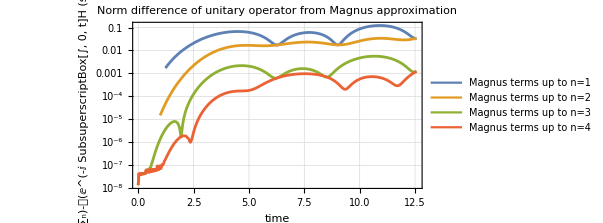

```mathematica
Legended[Show[Table[LogPlot[Norm[MatrixExp[Ωn[[j]]]-u[t]],{t,10^-3,tf},PlotStyle->ColorData[97][j]],{j,4}],PlotRange->All,GridLines->Automatic,PlotLabel->"Norm difference of unitary operator from Magnus approximation",AspectRatio->1/2,Frame->True,FrameLabel->{"time", "||ⅇ^(∑_n)-𝒯(ⅇ^(-ⅈ SubsuperscriptBox[∫, 0, t]H (s) ⅆs))||"}],Placed[LineLegend[Table[ColorData[97][j],{j,4}],Table["Magnus terms up to n="<>ToString[j],{j,4}]],{Right,Bottom}]]
```

## Source & Additional Information

### Contributed By

Mads Bahrami

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.